# Damped N-tuple Pendulum Tree

## Alexandre Khae Wu Navarro

This notebook executes the symbolic manipulations to obtain the damped n-tuple pendulum tree equations using the Hamiltonian formalism for dynamical systems.

TO DO:
- Change indexing to match parents

## System Generation

```mathematica
Clear["Global`*"]
```

Problem parameters:

```mathematica
n = 3;
L = Table[Subscript[l, i],{i, 1, n}];
M = Table[Subscript[m, i],{i, 1, n}];
```

Problem variables:

```mathematica
angles = Table[Subscript[θ, i][t],{i, 1, n}];
dangles = Table[Subscript[θ, i]'[t],{i, 1, n}];
momenta = Table[Subscript[p, i][t],{i, 1, n}];
x = Table[Sum[Subscript[l, i] Sin[Subscript[θ, i][t]],{i, 1, j}],{j, 1, n}];
y = Table[-Sum[Subscript[l, i] Cos[Subscript[θ, i][t]],{i, 1, j}],{j, 1, n}];
dx = D[x,t];
dy = D[y,t];
```

Energy equations and Lagrangian:

```mathematica
T = Sum[g*M[[i]]*y[[i]],{i,1,n}];
V = Sum[1/2 * M[[i]]*(dx[[i]]^2+dy[[i]]^2),{i,1, n}];
Q = Sum[1/2*Subscript[d, i]*Subscript[θ, i]'[t]^2,{i, 1, n}];
Lagrangian = T - (V + Q);
```

Hamiltonian and differential equations for the angles and momentum:
dθ_i/dt=(∂H)/(∂p_i) and dp_i/dt=-(∂H)/(∂θ_i)

```mathematica
pTable=Table[D[Lagrangian,Subscript[θ, i]'[t]],{i,1,n}]//Simplify//Flatten;
Hamiltonian  = Sum[Subscript[p, i][t]*Subscript[θ, i]'[t],{i,1,n}] - Lagrangian;
dthetaTable = Solve[pTable==momenta,dangles]//Simplify//Flatten;
Hamiltonian = Hamiltonian /.dthetaTable;
dpTable = Table[Subscript[p, i]'[t]->-D[Hamiltonian,Subscript[θ, i][t]],{i,1,n}]//Flatten;
system = Union[dthetaTable,dpTable];
(*Some string manipulation to change rule operation to equality*)
systemString = system//FullForm// ToString;
system = StringReplace[systemString, "Rule" -> "Equal"] // ToExpression ;
system//TraditionalForm
```

{p_1'(t)==-1/(l_1^2 l_3^2 m_3^2)d_3 tan(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))^2 sec^2(θ_1(t)-θ_3(t))-1/(l_1^2 l_3^2 m_3^2)d_3 (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))) ((cos(θ_1(t)-θ_2(t)) cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)) sec^2(θ_1(t)-θ_3(t))-1/(l_1 l_3 m_3)tan(θ_1(t)-θ_3(t)) p_3(t) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))) sec(θ_1(t)-θ_3(t))-1/(l_1 l_3 m_3)p_3(t) ((cos(θ_1(t)-θ_2(t)) cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)) sec(θ_1(t)-θ_3(t))+(d_1 (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3+(d_2 l_1^2 ((2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 m_3 (m_2+m_3) l_3^2+2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t))))^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^3+g sin(θ_1(t)) l_1 m_1+g sin(θ_1(t)) l_1 m_2+g sin(θ_1(t)) l_1 m_3+(p_1(t) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))-((-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) p_1(t) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2-(d_1 (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2-1/2 m_1 (-(2 cos^2(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2 l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3-(2 sin^2(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2 l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3+(2 cos^2(θ_1(t)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(2 sin^2(θ_1(t)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)-(p_2(t) (l_3 m_3 ((l_2 (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)+cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3-sin(θ_1(t)-θ_2(t)) m_2) p_1(t) l_1)-sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))+(l_1^2 ((2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 m_3 (m_2+m_3) l_3^2+2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2) p_2(t) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(d_2 (l_3 m_3 ((l_2 (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)+cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3-sin(θ_1(t)-θ_2(t)) m_2) p_1(t) l_1)-sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-1/2 m_2 (2 (-(cos(θ_2(t)) l_2 ((2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 m_3 (m_2+m_3) l_3^2+2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))) l_1^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(cos(θ_1(t)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(cos(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(cos(θ_2(t)) l_2 (l_3 m_3 ((l_2 (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)+cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3-sin(θ_1(t)-θ_2(t)) m_2) p_1(t) l_1)-sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))) ((cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(cos(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+2 (-(sin(θ_2(t)) l_2 ((2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 m_3 (m_2+m_3) l_3^2+2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))) l_1^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(sin(θ_1(t)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))-(cos(θ_1(t)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(sin(θ_2(t)) l_2 (l_3 m_3 ((l_2 (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)+cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3-sin(θ_1(t)-θ_2(t)) m_2) p_1(t) l_1)-sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))) ((sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))-1/2 m_3 (2 (-(cos(θ_2(t)) l_2 ((2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 m_3 (m_2+m_3) l_3^2+2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))) l_1^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(cos(θ_1(t)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(cos(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(cos(θ_2(t)) l_2 (l_3 m_3 ((l_2 (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)+cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3-sin(θ_1(t)-θ_2(t)) m_2) p_1(t) l_1)-sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))+1/(m_3 l_1)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) tan(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+1/(m_3 l_1)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) ((cos(θ_1(t)-θ_2(t)) cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2))) (-(cos(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+(cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3))))+2 (-(sin(θ_2(t)) l_2 ((2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 m_3 (m_2+m_3) l_3^2+2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))) l_1^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(sin(θ_1(t)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))-(cos(θ_1(t)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(sin(θ_2(t)) l_2 (l_3 m_3 ((l_2 (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)+cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3-sin(θ_1(t)-θ_2(t)) m_2) p_1(t) l_1)-sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))+1/(m_3 l_1)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) tan(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+1/(m_3 l_1)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) ((cos(θ_1(t)-θ_2(t)) cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (sin(θ_1(t)-θ_3(t)) l_1 l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_2(t)-l_2 (sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2+sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_1^2-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) l_2^2-(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(-cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) l_2^2-sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2))) (-(sin(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+(sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3))))),p_2'(t)==-1/(l_1^2 l_3^2 m_3^2)d_3 (-(cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)+(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+((cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) ((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))) sec^2(θ_1(t)-θ_3(t))-1/(l_1 l_3 m_3)p_3(t) (-(cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)+(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+((cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) ((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)) sec(θ_1(t)-θ_3(t))+(d_1 (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3+(d_2 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_3^2 m_3^2 l_2^2+l_1^2 (l_3^2 m_3 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_1 m_3-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 (m_2+m_3))-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t))))^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^3+g sin(θ_2(t)) l_2 m_2+g sin(θ_2(t)) l_2 m_3+(p_1(t) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))-((-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) p_1(t) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2-(d_1 (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2-(p_2(t) (sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)+l_3 m_3 (l_2 (-sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t) l_1^2+l_2 l_3 (sin(θ_1(t)-θ_2(t)) m_2+cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3) p_1(t) l_1-sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-1/2 m_1 (-(2 cos^2(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2 l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3-(2 sin^2(θ_1(t)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2 l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3+(2 cos^2(θ_1(t)) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(2 sin^2(θ_1(t)) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)+((2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_3^2 m_3^2 l_2^2+l_1^2 (l_3^2 m_3 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_1 m_3-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 (m_2+m_3))-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2) p_2(t) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(d_2 (sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)+l_3 m_3 (l_2 (-sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t) l_1^2+l_2 l_3 (sin(θ_1(t)-θ_2(t)) m_2+cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3) p_1(t) l_1-sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t))) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-1/2 m_2 (2 ((cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(cos(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))) (-(cos(θ_1(t)) l_1 (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(cos(θ_1(t)) l_1 (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(cos(θ_2(t)) l_2 (sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)+l_3 m_3 (l_2 (-sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t) l_1^2+l_2 l_3 (sin(θ_1(t)-θ_2(t)) m_2+cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3) p_1(t) l_1-sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(cos(θ_2(t)) l_2 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_3^2 m_3^2 l_2^2+l_1^2 (l_3^2 m_3 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_1 m_3-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 (m_2+m_3))-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2)+2 (-(sin(θ_1(t)) l_1 (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) l_1 (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(sin(θ_2(t)) l_2 (sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)+l_3 m_3 (l_2 (-sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t) l_1^2+l_2 l_3 (sin(θ_1(t)-θ_2(t)) m_2+cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3) p_1(t) l_1-sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))+(cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_2(t)) l_2 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_3^2 m_3^2 l_2^2+l_1^2 (l_3^2 m_3 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_1 m_3-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 (m_2+m_3))-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2) ((sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))-1/2 m_3 (2 (-(cos(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+(cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))) (-(cos(θ_1(t)) l_1 (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(cos(θ_1(t)) l_1 (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(cos(θ_2(t)) l_2 (sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)+l_3 m_3 (l_2 (-sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t) l_1^2+l_2 l_3 (sin(θ_1(t)-θ_2(t)) m_2+cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3) p_1(t) l_1-sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))+1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) (-(cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)+(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+((cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) ((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2))-(sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(cos(θ_2(t)) l_2 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_3^2 m_3^2 l_2^2+l_1^2 (l_3^2 m_3 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_1 m_3-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 (m_2+m_3))-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2)+2 (-(sin(θ_1(t)) l_1 (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) l_1 (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(sin(θ_2(t)) l_2 (sin(θ_1(t)-θ_2(t)) d_3 l_1 l_2 (m_2+m_3) p_1(t)+l_3 m_3 (l_2 (-sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t) l_1^2+l_2 l_3 (sin(θ_1(t)-θ_2(t)) m_2+cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3) p_1(t) l_1-sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))+1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) (-(cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) p_1(t) l_2^2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)+(2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_2^2)/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(sin(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)) l_2)/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-sin(θ_2(t)-θ_3(t)) (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) p_1(t) l_2^2-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)) l_2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+((cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)-cos(θ_1(t)-θ_2(t)) sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) ((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2-sin(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_1^2 (m_2+m_3)-sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+(cos(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2))+(cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_2(t)) l_2 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_3^2 m_3^2 l_2^2+l_1^2 (l_3^2 m_3 (2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_1 m_3-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) m_2 (m_2+m_3))-2 cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_2(t)) d_3 (m_2+m_3)^2) l_2^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2) (-(sin(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+(sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3))))),p_3'(t)==1/(l_1^2 l_3^2 m_3^2)d_3 tan(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))^2 sec^2(θ_1(t)-θ_3(t))-1/(l_1^2 l_3^2 m_3^2)d_3 (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))) ((cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2 p_1(t)-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 tan(θ_1(t)-θ_3(t)) p_1(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)) sec^2(θ_1(t)-θ_3(t))+1/(l_1 l_3 m_3)tan(θ_1(t)-θ_3(t)) p_3(t) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))) sec(θ_1(t)-θ_3(t))-1/(l_1 l_3 m_3)p_3(t) ((cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2 p_1(t)-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 tan(θ_1(t)-θ_3(t)) p_1(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)) sec(θ_1(t)-θ_3(t))+(d_1 (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3+(d_2 (l_1^2 (-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 l_3^2 m_1 m_3^2)-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_2^2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t))))^2)/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^3+g sin(θ_3(t)) l_3 m_3+(p_1(t) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))-((-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) p_1(t) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2-(d_1 (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2-(l_3 m_3 p_2(t) ((2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)+l_2 (sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)) p_3(t)) l_1^2+l_2 l_3 (-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-1/2 m_1 (-(2 cos^2(θ_1(t)) (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2 l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3-(2 sin^2(θ_1(t)) (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))^2 l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^3+(2 cos^2(θ_1(t)) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(2 sin^2(θ_1(t)) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))) l_1^2)/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2)+((l_1^2 (-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 l_3^2 m_1 m_3^2)-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_2^2 l_3^2 m_3^2) p_2(t) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-(d_2 l_3 m_3 ((2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)+l_2 (sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)) p_3(t)) l_1^2+l_2 l_3 (-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t)) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2-1/2 m_2 (2 (-(cos(θ_1(t)) l_1 (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(cos(θ_1(t)) l_1 (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(cos(θ_2(t)) l_2 l_3 m_3 ((2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)+l_2 (sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)) p_3(t)) l_1^2+l_2 l_3 (-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(cos(θ_2(t)) l_2 (l_1^2 (-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 l_3^2 m_1 m_3^2)-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_2^2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2) ((cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(cos(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+2 (-(sin(θ_1(t)) l_1 (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) l_1 (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(sin(θ_2(t)) l_2 l_3 m_3 ((2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)+l_2 (sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)) p_3(t)) l_1^2+l_2 l_3 (-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_2(t)) l_2 (l_1^2 (-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 l_3^2 m_1 m_3^2)-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_2^2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2) ((sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-(sin(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))-1/2 m_3 (2 (-(cos(θ_1(t)) l_1 (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(cos(θ_1(t)) l_1 (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(cos(θ_2(t)) l_2 l_3 m_3 ((2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)+l_2 (sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)) p_3(t)) l_1^2+l_2 l_3 (-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) tan(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))-1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) ((cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2 p_1(t)-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 tan(θ_1(t)-θ_3(t)) p_1(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2))-(cos(θ_2(t)) l_2 (l_1^2 (-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 l_3^2 m_1 m_3^2)-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_2^2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2) (-(cos(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+(cos(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3))))+2 (-(sin(θ_1(t)) l_1 (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+(sin(θ_1(t)) l_1 (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2+(sin(θ_2(t)) l_2 l_3 m_3 ((2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3 m_3 p_2(t)+l_2 (sin(θ_2(t)-θ_3(t)) m_1-cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3)) p_3(t)) l_1^2+l_2 l_3 (-cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) m_3-cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+sin(θ_2(t)-θ_3(t)) d_1 l_2 p_3(t)))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))-1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) tan(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+1/(l_1 m_3)cos(θ_3(t)) sec(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) ((cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (sec(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2 p_1(t)-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 tan(θ_1(t)-θ_3(t)) p_1(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-l_2 (cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (sin(θ_1(t)-θ_3(t)) l_1 p_2(t)-sin(θ_2(t)-θ_3(t)) l_2 p_1(t))+sin(θ_1(t)-θ_3(t)) l_1 l_3 m_3 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) p_3(t)+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2-sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) (m_2+m_3) tan(θ_1(t)-θ_3(t)) l_2^2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)^2 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))))+(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) (-(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_3^2 m_3^2+cos(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_3^2 m_3^2) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2-(cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+sin(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)) l_2^2+2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2 (cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3))+(cos(θ_2(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) (m_2+m_3) l_2^2+sin(θ_1(t)-θ_3(t)) d_2) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))^2))-(sin(θ_2(t)) l_2 (l_1^2 (-2 cos(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_3(t)) d_2 l_3^2 m_3^2-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) l_2^2 l_3^2 m_1 m_3^2)-2 cos(θ_2(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) d_1 l_2^2 l_3^2 m_3^2) (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3)))^2) (-(sin(θ_1(t)) l_1 ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))+1/(l_1 m_3)sec(θ_1(t)-θ_3(t)) sin(θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))+(sin(θ_2(t)) l_2 (d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t)))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3))))),θ_1'(t)==-((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t)))/((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1))),θ_2'(t)==(d_3 (-(m_1+m_2+m_3) p_2(t) l_1^2+cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) p_1(t) l_1-d_1 p_2(t))+l_3 m_3 ((l_2 (cos(θ_2(t)-θ_3(t)) m_1+sin(θ_1(t)-θ_2(t)) sin(θ_1(t)-θ_3(t)) (m_2+m_3)) p_3(t)-l_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) p_2(t)) l_1^2+l_2 l_3 (cos(θ_1(t)-θ_2(t)) m_2+sin(θ_1(t)-θ_3(t)) sin(θ_2(t)-θ_3(t)) m_3) p_1(t) l_1+d_1 (cos(θ_2(t)-θ_3(t)) l_2 p_3(t)-l_3 p_2(t))))/(((l_3^2 m_3 (m_2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))+m_1 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2))-1/2 d_3 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_2^2+d_2 (m_3 (m_3 sin^2(θ_1(t)-θ_3(t))+m_1+m_2) l_3^2+d_3 (m_1+m_2+m_3))) l_1^2+d_1 ((m_3 (m_3 sin^2(θ_2(t)-θ_3(t))+m_2) l_3^2+d_3 (m_2+m_3)) l_2^2+d_2 (m_3 l_3^2+d_3))),θ_3'(t)==1/(l_1 l_3 m_3)sec(θ_1(t)-θ_3(t)) (-p_1(t)+(cos(θ_1(t)-θ_2(t)) l_2 (m_2+m_3) (cos(θ_2(t)-θ_3(t)) sec(θ_1(t)-θ_3(t)) l_2 p_1(t)-l_1 p_2(t)))/(sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2)-(((d_2 (m_1+m_2+m_3)-1/2 l_2^2 (m_2+m_3) (-2 (m_2+m_3) sin^2(θ_1(t)-θ_2(t))-2 m_1)) l_1^2+d_1 ((m_2+m_3) l_2^2+d_2)) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos(θ_1(t)-θ_3(t)) l_1 l_3 m_3 p_3(t)-(m_3 l_3^2+d_3) p_1(t))-l_2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_3(t)) l_1 p_2(t)-cos(θ_2(t)-θ_3(t)) l_2 p_1(t))))/((sec(θ_1(t)-θ_3(t)) sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)-d_2) ((cos(θ_1(t)-θ_3(t)) d_2-sin(θ_1(t)-θ_2(t)) sin(θ_2(t)-θ_3(t)) l_2^2 (m_2+m_3)) (cos^2(θ_1(t)-θ_3(t)) l_1^2 l_3^2 m_3^2-(-m_3 l_3^2-d_3) (-(m_1+m_2+m_3) l_1^2-d_1))-l_2^2 (cos(θ_1(t)-θ_3(t)) cos(θ_2(t)-θ_3(t)) l_3^2 m_3^2-cos(θ_1(t)-θ_2(t)) (m_2+m_3) (m_3 l_3^2+d_3)) (cos(θ_1(t)-θ_2(t)) cos(θ_1(t)-θ_3(t)) (m_2+m_3) l_1^2+cos(θ_2(t)-θ_3(t)) (-(m_1+m_2+m_3) l_1^2-d_1)))))}

## Simulation

Set system parameters to a given value

```mathematica
g =9.8;
valuesL = Table[L[[i]]->2.,{i, 1, n}];
valuesM= Table[M[[i]]->1.,{i, 1, n}];
valuesD= Table[Subscript[d, i]->10.,{i, 1, n}];
parameterValues = Union[valuesL,valuesM,valuesD];
finalTime = 180;
```

```mathematica
odes = system/.parameterValues ;
```

Define boundary conditions

```mathematica
thetaBoundaryValues = Table[π/5 ,{i,1,n}];
dthetaBoundaryValues = Table[0.,{i,1,n}];
thetaBoundaryTable = Table[Subscript[θ, i][0] == thetaBoundaryValues[[i]],{i,1,n}];
momentaThetaBoundary = Table[Subscript[θ, i][t] -> thetaBoundaryValues[[i]],{i,1,n}];
momentaDThetaBoundary = Table[Subscript[θ, i]'[t] -> dthetaBoundaryValues[[i]],{i,1,n}];
pBoundaryValues =pTable/.parameterValues/.momentaThetaBoundary/.momentaDThetaBoundary;
pBoundaryTable = Table[Subscript[p, i][0]==pBoundaryValues[[i]],{i,1,n}];
boundaryConditions = Union[thetaBoundaryTable, pBoundaryTable];
```

Evaluate numerically

```mathematica
variables = Union[Table[Subscript[p, i],{i,1,n}],Table[Subscript[θ, i],{i,1,n}]];
solutions = NDSolve[Union[odes, boundaryConditions],variables,{t, finalTime}];
```

```mathematica
data = Table[Evaluate[angles/.Flatten[solutions]],{t, 0, finalTime, 0.1}];
```

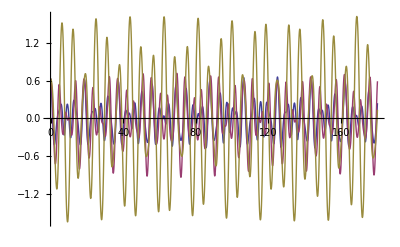

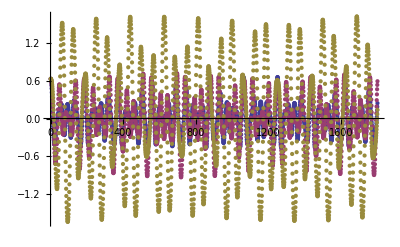

```mathematica
Plot[Evaluate[angles/.solutions],{t,0,finalTime},PlotRange->All]
ListPlot[Transpose[data]]
```

```mathematica
xData=Table[Sum[L[[i]] * Sin[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
yData=Table[Sum[-L[[i]] * Cos[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
```

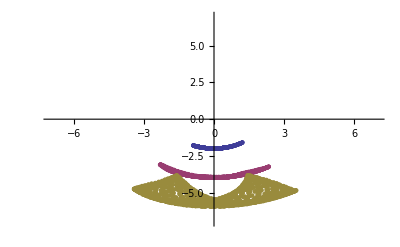

```mathematica
ListPlot[{Transpose[{xData[[1]],yData[[1]]}],Transpose[{xData[[2]],yData[[2]]}],Transpose[{xData[[3]],yData[[3]]}]},PlotRange->{{-7,7},{-7,7}}]
```

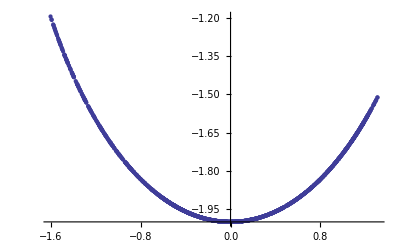

```mathematica
ListPlot[Transpose[{xData[[2]] - xData[[1]],yData[[2]]-yData[[1]]}]]
```

```mathematica
Export["./dampedNtuplePendulum_"<>ToString[n]<>"_dim.csv",Union[xData,yData]];
```

Define boundary conditions for Chaotic Pendulum

```mathematica
thetaBoundaryValues = Table[π/2 ,{i,1,n}];
dthetaBoundaryValues = Table[0.,{i,1,n}];
thetaBoundaryTable = Table[Subscript[θ, i][0] == thetaBoundaryValues[[i]],{i,1,n}];
momentaThetaBoundary = Table[Subscript[θ, i][t] -> thetaBoundaryValues[[i]],{i,1,n}];
momentaDThetaBoundary = Table[Subscript[θ, i]'[t] -> dthetaBoundaryValues[[i]],{i,1,n}];
pBoundaryValues =pTable/.parameterValues/.momentaThetaBoundary/.momentaDThetaBoundary;
pBoundaryTable = Table[Subscript[p, i][0]==pBoundaryValues[[i]],{i,1,n}];
boundaryConditions = Union[thetaBoundaryTable, pBoundaryTable];
```

Evaluate numerically

```mathematica
variables = Union[Table[Subscript[p, i],{i,1,n}],Table[Subscript[θ, i],{i,1,n}]];
solutions = NDSolve[Union[odes, boundaryConditions],variables,{t, finalTime}];
```

```mathematica
data = Table[Evaluate[angles/.Flatten[solutions]],{t, 0, finalTime, 0.1}];
```

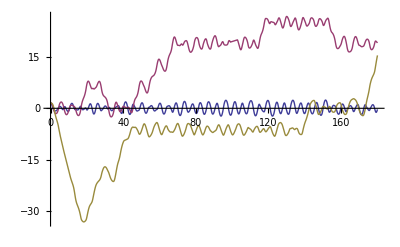

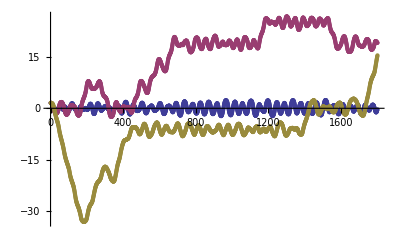

```mathematica
Plot[Evaluate[angles/.solutions],{t,0,finalTime},PlotRange->All]
ListPlot[Transpose[data]]
```

```mathematica
xData=Table[Sum[L[[i]] * Sin[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
yData=Table[Sum[-L[[i]] * Cos[Transpose[data][[i]]]/.valuesL[[i]],{i,1,j}],{j,1,n}];
```

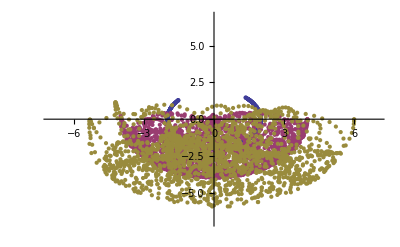

```mathematica
ListPlot[{Transpose[{xData[[1]],yData[[1]]}],Transpose[{xData[[2]],yData[[2]]}],Transpose[{xData[[3]],yData[[3]]}]},PlotRange->{{-7,7},{-7,7}}]
```

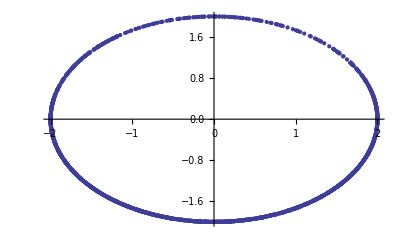

```mathematica
ListPlot[Transpose[{xData[[2]] - xData[[1]],yData[[2]]-yData[[1]]}]]
```

```mathematica
Export["./chaoticNtuplePendulum_"<>ToString[n]<>"_dim.csv",Union[xData,yData]];
```